```mathematica
FullSimplify[(E^(I x )+ 9E^(-I x ))/2]
```

5 Cos[x]-4 ⅈ Sin[x]

```mathematica
FullSimplify[Gamma[s/2]Gamma[s/2]]
```

Gamma[s/2]^2

```mathematica
pa11[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
```

```mathematica
pa11[100000,.23+12I]
```

1.05615-0.90073 ⅈ

```mathematica
Zeta[.23+12I]
```

1.05611-0.900568 ⅈ

```mathematica
pa1[n_,s_]:= (1/2)Pi^(-s/2)s(s-1)Gamma[s/2](n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
pa2[n_,s_]:= (1/2)Pi^(-s/2)Gamma[s/2](n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(2^(1-s) n^(1-s) π^-s Cos[(π s)/2] Gamma[s]/(s-1)-n^s  /s)
pa3[n_,s_]:= (1/2)Gamma[s/2](n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(2^(1-s) n^(1-s) π^(-s/2)Cos[(π s)/2] Gamma[s]/(s-1)-n^s  /s Pi^(s/2))
pa4[n_,s_]:= Gamma[s/2](n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(2^(2-s) n^(1-s) π^(-s/2)Cos[(π s)/2] Gamma[s]/(s-1)-2 n^s  /s Pi^(s/2))
pa5[n_,s_]:= Gamma[s/2](n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(2^(2-s) n^(1-s) π^(-s/2)Cos[(π s)/2] (Gamma[s/2]Gamma[(s+1)/2]/(2^(1-s) Pi^(1/2)))/(s-1)-2 n^s  /s Pi^(s/2))
pa6[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(2/Gamma[s/2] n^(1-s) π^(-(s+1)/2) Cos[(π s)/2] (Gamma[s/2]Gamma[(s+1)/2])/(s-1)-2 n^s  /s Pi^(s/2)/Gamma[s/2])
pa7[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])/(2 n^(1-s) π^(-(s+1)/2) Cos[(π s)/2] Gamma[(s+1)/2]/(s-1)-2 n^s  /s Pi^(s/2)/Gamma[s/2])
```

```mathematica
pa7[100000,.23+12I]
```

0.00864027-0.00222696 ⅈ

```mathematica
(1/2)Pi^(-s/2)s(s-1)Gamma[s/2]Zeta[s]/.s->.23+12I
```

0.00863991-0.00218371 ⅈ

```mathematica
Expand[π^(-s/2)/ Pi^(1/2)]
```

π^(-1/2-s/2)

```mathematica
ps5[n_,s_]:= ((2^s Pi^(s-1) Sin[ Pi s / 2] Gamma[1-s])+(s/(s-1)) n^(1-2s)) Zeta[1-s]-(HarmonicNumber[n,s]+(s/(s-1)) n^(1-2s)HarmonicNumber[n,1-s])
ps5a[n_,s_]:= ((2^s Pi^(s-1) Sin[ Pi s / 2] Gamma[1-s]n^s (s-1))+s n^(1-s)) Zeta[1-s]-((s-1)n^s HarmonicNumber[n,s]+s n^(1-s)HarmonicNumber[n,1-s])
ps5b[n_,s_]:= ((s-1)n^s HarmonicNumber[n,s]+s n^(1-s)HarmonicNumber[n,1-s])/((2^s Pi^(s-1) Sin[ Pi s / 2] Gamma[1-s]n^s (s-1))+s n^(1-s))
ps5x[n_,s_]:= ((2^(1-s) Pi^((1-s)-1) Sin[ Pi (1-s) / 2] Gamma[1-(1-s)])+((1-s)/((1-s)-1)) n^(1-2(1-s))) Zeta[1-(1-s)]-(HarmonicNumber[n,(1-s)]+((1-s)/((1-s)-1)) n^(1-2(1-s))HarmonicNumber[n,1-(1-s)])
```

```mathematica
ps5x[1000000000000,.3+2I]
```

-2.0091×10^-9+3.41047×10^-9 ⅈ

```mathematica
Zeta[1-(.3+2I)]
```

0.501262+0.334245 ⅈ

```mathematica
n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s]
```

n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s]

```mathematica
n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s]/.n->1000000/.s->N@ZetaZero@1
```

0.+14.1347 ⅈ

```mathematica
Integrate[ j^-s,{j,0,n}]
```

ConditionalExpression[-n^(1-s)/(-1+s),Re[s]<1]

```mathematica
n^(1-s) s Sum[j^(s-1),{j,1,n}]-n^s (1-s) Sum[j^-s,{j,1,n}]/.n->10000000/.s->N@ZetaZero@1
```

0.+14.1347 ⅈ

```mathematica
FullSimplify[n^(1-s) s Integrate[j^(s-1),{j,0,n}]-n^s (1-s) Integrate[j^-s,{j,0,n}]]
```

ConditionalExpression[0,0<Re[s]<1]

```mathematica
FullSimplify[n^(1/2-s) s Integrate[j^(s-1),{j,0,n}]-n^(s-1/2) (1-s) Integrate[j^-s,{j,0,n}]]
```

ConditionalExpression[0,0<Re[s]<1]

```mathematica
FullSimplify[ Integrate[s (n/j)^(1-s),{j,0,n}]-(1-s) Integrate[(n/j)^s,{j,0,n}]]
```

ConditionalExpression[0,0<Re[s]<1&&n>0]

```mathematica
Integrate[s (n/j)^(1-s),{j,0,n}]
```

ConditionalExpression[n,Re[s]>0&&n>0]

```mathematica
FullSimplify[(1-s) Integrate[(n/j)^s,{j,0,n}]]
```

ConditionalExpression[n,Re[s]<1&&n>0]

```mathematica
bb[n_,s_]:= (1-s) Sum[(n/j)^s,{j,1,n}]
bba[n_,s_]:= (1-s) Sum[E^(s Log[n/j]),{j,1,n}]
bba2[n_,s_,t_]:= (1-s-t I) Sum[E^((s+t I) Log[n/j]),{j,1,n}]
bba3[n_,s_,t_]:= (1-s-t I) Sum[(n/j)^s E^(I t  Log[n/j]),{j,1,n}]
bba4[n_,s_,t_]:= (1-s-t I) Sum[(n/j)^s (Cos[t  Log[n/j]]+I Sin[t  Log[n/j]]),{j,1,n}]
bba5[n_,s_,t_]:= (1-s) Sum[(n/j)^s (Cos[t  Log[n/j]]+I Sin[t  Log[n/j]]),{j,1,n}]-t I Sum[(n/j)^s (Cos[t  Log[n/j]]+I Sin[t  Log[n/j]]),{j,1,n}]
bba6[n_,s_,t_]:= (1-s) Sum[(n/j)^s (Cos[t  Log[n/j]]),{j,1,n}]-t I Sum[(n/j)^s (Cos[t  Log[n/j]]),{j,1,n}]+(1-s) Sum[(n/j)^s (I Sin[t  Log[n/j]]),{j,1,n}]-t I Sum[(n/j)^s (I Sin[t  Log[n/j]]),{j,1,n}]
bba7[n_,s_,t_]:= (1-s) Sum[(n/j)^s Cos[t  Log[n/j]],{j,1,n}]-t I Sum[(n/j)^s Cos[t  Log[n/j]],{j,1,n}]+(1-s) Sum[(n/j)^s  I Sin[t  Log[n/j]],{j,1,n}]-t I Sum[(n/j)^s  I Sin[t  Log[n/j]],{j,1,n}]
bba8[n_,s_,t_]:=  Sum[(n/j)^s (1-s)Cos[t  Log[n/j]],{j,1,n}]+Sum[(n/j)^s  t Sin[t  Log[n/j]],{j,1,n}]-I Sum[(n/j)^s t Cos[t  Log[n/j]],{j,1,n}]+I Sum[(n/j)^s (1-s) Sin[t  Log[n/j]],{j,1,n}]
bba9[n_,s_,t_]:=  Sum[(n/j)^s ((1-s)Cos[t  Log[n/j]]+ t Sin[t  Log[n/j]]),{j,1,n}]-I Sum[(n/j)^s (t Cos[t  Log[n/j]]-(1-s) Sin[t  Log[n/j]]),{j,1,n}]
bba9a[n_,s_,t_]:=Sum[(n/j)^s ((1-s)Cos[t  Log[n/j]]+ t Sin[t  Log[n/j]]),{j,1,n}]
bba9b[n_,s_,t_]:=2Sum[(n/j)^s (t Cos[t  Log[n/j]]-(1-s) Sin[t  Log[n/j]]),{j,1,n}]
bb2[n_,s_]:=s Sum[(n/j)^(1-s),{j,1,n}]
```

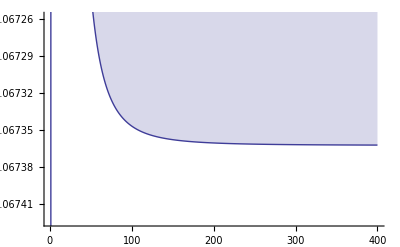

```mathematica
DiscretePlot[Im@(bba9[n,.5,N@Im@ZetaZero@1]),{n,1,400}]
```

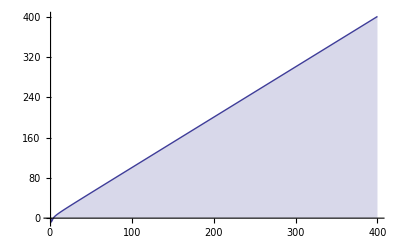

```mathematica
DiscretePlot[bba9a[n,.5,N@Im@ZetaZero@1],{n,1,400}]
```